# Žrtve prometnih nesreč v Ameriki in po svetu

## Pripravil: Nejc Čeh, ROM 2022/23

## PRIDOBIVANJE PODATKOV

Vsi podatki so bili pridobljeni z naslednjih spletnih strani. Podatke sem prenesel s programom Excel, kjer sem jih tudi uredil, tako da sem jih lahko uporabil v temu programu, torej  Wolfram Mathematica.

```mathematica
Hyperlink["https://injuryfacts.nsc.org/motor-vehicle/historical-fatality-trends/deaths-and-rates/"]
```

https://injuryfacts.nsc.org/motor-vehicle/historical-fatality-trends/deaths-and-rates/

```mathematica
Hyperlink["https://www.iihs.org/topics/fatality-statistics/detail/yearly-snapshot"]
```

https://www.iihs.org/topics/fatality-statistics/detail/yearly-snapshot

```mathematica
Hyperlink["https://injuryfacts.nsc.org/motor-vehicle/overview/type-of-crash/"]
```

https://injuryfacts.nsc.org/motor-vehicle/overview/type-of-crash/

```mathematica
Hyperlink["https://worldpopulationreview.com/country-rankings/countries-with-the-most-car-accidents"]
```

https://worldpopulationreview.com/country-rankings/countries-with-the-most-car-accidents

```mathematica
Hyperlink["https://www.iihs.org/topics/fatality-statistics/detail/males-and-females"]
```

```mathematica
["https://www.iihs.org/topics/fatality-statistics/detail/males-and-females"](https://www.iihs.org/topics/fatality-statistics/detail/males-and-females)
```

```mathematica
Hyperlink["https://injuryfacts.nsc.org/motor-vehicle/historical-fatality-trends/deaths-by-age-group/"]
```

```mathematica
"https://injuryfacts.nsc.org/motor-vehicle/historical-fatality-trends/deaths-by-age-group/"https://injuryfacts.nsc.org/motor-vehicle/historical-fatality-trends/deaths-by-age-group/Nonehttps://injuryfacts.nsc.org/motor-vehicle/historical-fatality-trends/deaths-by-age-group/HyperlinkActionRecycledHyperlinkActive
```

## UVOD

V projektni nalogi si bomo ogledali prometne nesreče. Ker pa je Amerika, oziroma država Združenih držav Amerike najbolj prometna država na svetu, si bomo za veliko primerjav ogledali ravno njo. Tako bomo raziskali, kolikšen procent nesreč je smrtnih, kakšno povezavo imajo prometne nesreče s starostjo in pa spolom, katere države imajo največ prometnih nesreč glede na število prebivalcev in podobno.

## SMRTNE ŽRTVE PROMETNIH NESREČ V ZDA

```mathematica
podatki1 = Import["C:\\Rac_praktikum\\Motor-Vehicle Deaths and Rates.xlsx", "Dataset", "HeaderLines"->1]//First
```

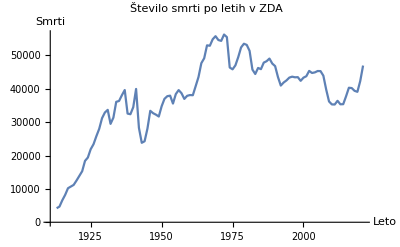

```mathematica
extractedData=podatki1[[All,{1,2}]];
ListLinePlot[extractedData,PlotLabel->"Število smrti po letih v ZDA",PlotLegends->Placed[Automatic,{0.75,0.75}], AxesLabel->{"Leto", "Smrti"}]
```

Na prvi pogled se zdijo ti podatki z grafa malo čudni, saj število nesreč, oziroma smrtnih žrtev narašča. Upoštevati pa je potrebno, da je tudi število voznikov, oziroma vozil na cesti naraslo. Zato si lahko ogledamo še število smrti na 10 000 vozil na cesti.

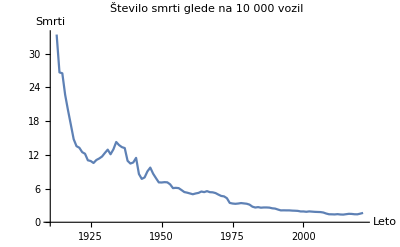

```mathematica
extractedData2 = podatki1[[All,{1,4}]];
ListLinePlot[extractedData2,PlotLabel->"Število smrti glede na 10 000 vozil",PlotLegends->Placed[Automatic,{0.75,0.75}], AxesLabel->{"Leto", "Smrti"}]
```

## PROCENT SMRTNOSTI NESREČ

```mathematica
podatki2 = Import["C:\\Rac_praktikum\\StatistikaSmrti.xlsx", "Dataset", "HeaderLines"->1]//First
```

```mathematica
data={5400000,37750,3260000};
labels={"Nesmrtne nesreče","Smrtne nesreče","Nesreče s poškodbami"};
labelsWithPercentages=Tooltip[Row[{#1," ",#2}],#2]&@@@Transpose[{labels,data}];
PieChart3D[data,ChartLegends->labels,ChartLegends->Placed[labelsWithPercentages,"Right"],ChartStyle->"Pastel"]
```

-Graphics3D-

Tukaj je mogoče opaziti, da je zelo majhen procent nesreč dejansko smrtnih, oziroma zahteva smrtne žrtve. Od 13 204 000 nesreč, ki se zgodijo skozi leto, je zgolj 37 750 nesreč smrtnih, oziroma zahtevajo 46 980 smrtnih žrtev. Torej zgolj 0,286 % vseh nesreč zahtevajo smrtne žrtve. Sicer pa so podatki z leta 2018 ter gre za podatke v ZDA. Skozi leta pa se je ta procent zelo malo spreminjal.

## PROMETNE NESREČE PO SVETU

```mathematica
podatki3 = Import["C:\\Rac_praktikum\\NesrecePoSvetu.xlsx", "Dataset"]
```

{}

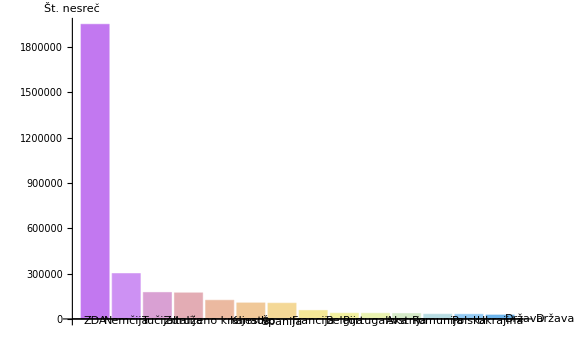

```mathematica
drzave = Table[podatki7[[1]][[i]][[1]], {i, 2, Length[podatki7[[1]]]}];
BarChart[{1949000,300143,174896,172183,123212,105791,104080,56006,37699,37213,35736,31146,30288,26052}, ChartLabels->{drzave},ImageSize->Large, AxesLabel->{"Država","Št. nesreč"},ChartStyle->"Pastel"]
```

Pridobljeni podatki so iz leta 2019. Tukaj je mogoče opaziti, da je v ZDA daleč nejveč prometnih nesreč. Presenetljivo pa je, da Kitajska, kot druga svetovna država z največ prometa (takoj za ZDA), ni na listi. Visoko na listi pa je tudi Rusija, vendar podatki niso popolnoma javno znani, zato ni vključena v listo.

Sedaj pa si lahko ogledamo še število nesreč in pa smrtnih žrtev, glede na milijon prebivalcev, kar bo nekoliko bolj realna številka. Opazili bomo, da se na listi znajde celo Slovenija.

```mathematica
podatki4 = Import["C:\\Rac_praktikum\\Book2.xlsx","Dataset", "HeaderLines"->1]
```

{,}

## STAROST SMRTNIH ŽRTEV PROMETNIH NESREČ, ZDA

```mathematica
podatki5 = Import["C:\\Rac_praktikum\\leta.xlsx", "Dataset", "HeaderLines"->1]//First
```

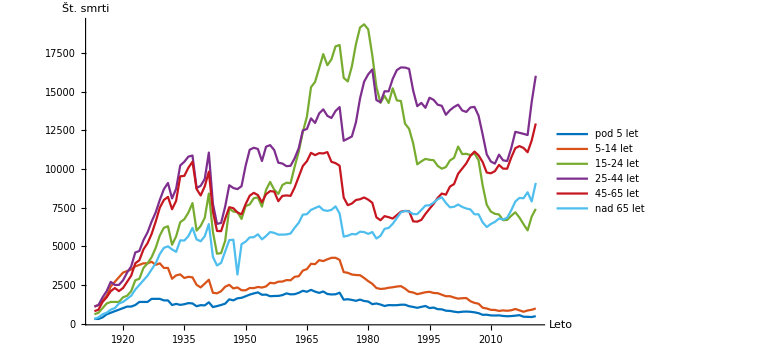

```mathematica
vrednost1=starost[[All, {1, 2}]];
vrednost2=starost[[All, {1,3}]];
vrednost3=starost[[All, {1,4}]];
vrednost4=starost[[All, {1,5}]];
vrednost5=starost[[All, {1,6}]];
vrednost6=starost[[All, {1,7}]];
graf1 = ListLinePlot[vrednost1, PlotStyle->RGBColor[0,0.447,0.741], PlotLegends->{"pod 5 let"}];
graf2 = ListLinePlot[vrednost2, PlotStyle-> RGBColor[0.85,0.325,0.098],PlotLegends->{"5-14 let"}];
graf3 = ListLinePlot[vrednost3, PlotStyle->RGBColor[0.466,0.674,0.188],PlotLegends->{"15-24 let"}];
graf4 = ListLinePlot[vrednost4, PlotStyle->RGBColor[0.494,0.184,0.556],PlotLegends->{"25-44 let"}];
graf5 = ListLinePlot[vrednost5, PlotStyle->RGBColor[0.776,0.086,0.125],PlotLegends->{"45-65 let"}];
graf6 = ListLinePlot[vrednost6, PlotStyle->RGBColor[0.301,0.745,0.933],PlotLegends->{"nad 65 let"}];
Show[graf1, graf2, graf3, graf4, graf5, graf6, PlotRange->Automatic, ImageSize->Large, AxesLabel->{"Leto", "Št. smrti"}]
```

#### Starost oseb, ki so vozile vozilo v prometni nesreči, ZDA, podatki 2021

```mathematica
podatki7 = Import["C:\\Rac_praktikum\\Book1.xlsx", "Dataset", "HeaderLines" -> 1]//First
```

Pri teh podatkih je mogoče videti, da čeprav največ nesreč povzročijo izkušeni vozniki, je to zgolj zaradi tega, ker jih je tudi največ. Če gledamo nesreče glede na 10 000 voznikov, lahko vidimo da z starostjo, število nesreč pada.

## ŽRTVE PROMETNIH NESREČ, SPOL; ZDA

```mathematica
podatki6 = Import["C:\\Rac_praktikum\\spol.xlsx", "Dataset", "HeaderLines" -> 1]//First
```

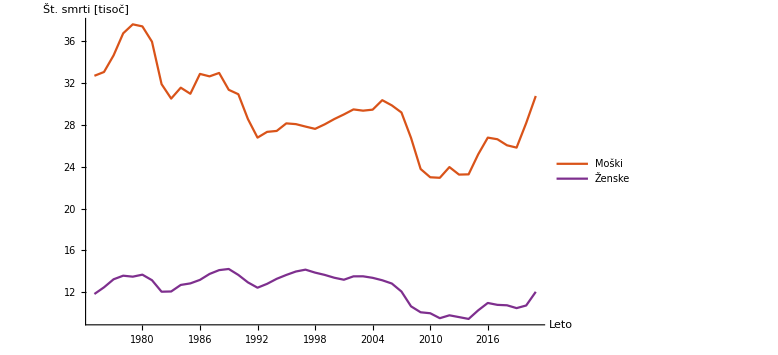

```mathematica
zenske = data10[[All, {1, 3}]];
moski = data10[[All, {1, 2}]];
graph1 = ListLinePlot[moski, PlotStyle->RGBColor[0.85,0.325,0.098],AxesOrigin->{1970, 0},  PlotLegends->{"Moški"}];
graph2 = ListLinePlot[zenske, PlotStyle->RGBColor[0.494,0.184,0.556],AxesOrigin->{1970, 0}, PlotLegends->{"Ženske"}];
Show[graph1, graph2, PlotRange->Automatic,  AxesLabel->{"Leto", "Št. smrti [tisoč]"},ImageSize->Large]
```